# 线性方程组的迭代解法

## 实验目的

编写线性方程组求解的几种常见迭代法的实现，包括Jacobi，G-S和SOR等三种方法。
并利用所得之程序求解上机题 2 中有关微分方程离散化的题目，将所得结果与精确解相比较。

## 算法原理与代码实现

防御性代码，清理执行环境

```mathematica
Clear["Global`*"]
```

矩阵的对角线可以使用Diagonal[]取得，相应之绝对上三角阵亦可以直接用UpperTrianglurize[]等内置函数取得。对于 Jacobi 迭代法，由于式中之 D 为对角阵，求逆之后直接使用矩阵相乘并不会增加运算量，因此可以简易实现如下。

```mathematica
jacobiSolve[x_List, a_List, b_List] := (*Solve Ax = b using Jacobi Method*)
Block[{D = DiagonalMatrix[1/Diagonal@a], LU =DiagonalMatrix@Diagonal@a-a},
NestWhile[N[D.LU.#+D.b]&,x (*使用幻灯片所给的矩阵公式*),(Min[Abs[#1-#2]/#1]<(10^-4/2))&,2(*要求四位有效数字*)]
]
```

对于 G-S 迭代法，对一个下三角阵求逆运用矩阵运算是相当不合理的。我们需要采用更直接的实现策略。 
题目中所给出的待求解矩阵 A 是一个 n=100 维的三对角稀疏矩阵，并且矩阵中有大量的重复元素，利用这个性质，我们可以对给定 ϵ,h 的值，直接写出计算迭代值的公式，应用到解向量上进行计算。这样可以加快运算速度。对于一般的稀疏矩阵问题，则可以通过生成代码的方式，根据输入的稀疏矩阵生成出迭代的公式，编译后进行迭代计算。

注意到所给的矩阵为三对角线上元素都相等的矩阵，因此可以直接利用迭代公式给出以下代码

```mathematica
jacobiSolve[ϵ_,h_,a_]:=Block[{x,b=a h^2,上一轮},
(*取初值*)
x[i_]:=0;上一轮[i_]:=0;
x[100]=1;上一轮[100]=1;
Do[x[i]=RandomReal[];,{i,0,99}];
Do[
Do[上一轮[i]=x[i],{i,0,99}];
Do[
x[i]=1/(-(2ϵ+h))(b-ϵ 上一轮[i-1]-(ϵ+h)上一轮[i+1]);
,{i,0,99}];

If[Max@Abs@Table[上一轮[i]/x[i]-1,{i,0,99}]<10^-4/2,
Print["迭代步数 = ",迭代步数];Return[Table[x[i],{i,0,99}]]]
,{迭代步数,100000}]

]
```

```mathematica
gsSolve[ϵ_,h_,a_]:=Block[{x,b=a h^2,上一轮},
(*取初值*)
x[i_]:=0;上一轮[i_]:=0;
x[100]=1;上一轮[100]=1;
Do[x[i]=RandomReal[];,{i,0,99}];
Do[上一轮[i]=2;,{i,0,99}];(*最开始判停条件不可能满足*)
Do[
Do[
x[i]=1/(-(2ϵ+h))(b-ϵ x[i-1]-(ϵ+h)x[i+1]);
,{i,0,99}];

If[Max@Abs@Table[上一轮[i]/x[i]-1,{i,0,99}]<10^-4/2,
Print["迭代步数 = ",迭代步数];Return[Table[x[i],{i,0,99}]],
Do[上一轮[i]=x[i],{i,0,99}];]
,{迭代步数,100000}]

]
```

```mathematica
sorSolve[ϵ_,h_,a_,ω_]:=Block[{x,b=a h^2,上一轮},
(*取初值*)
x[i_]:=0;上一轮[i_]:=0;
x[100]=1;上一轮[100]=1;
Do[x[i]=RandomReal[];,{i,0,99}];
Do[上一轮[i]=2;,{i,0,99}];(*最开始判停条件不可能满足*)
Do[
Do[
x[i]=(1-ω)x[i]+ω/(-(2ϵ+h))(b-ϵ x[i-1]-(ϵ+h)x[i+1]);
,{i,0,99}];

If[Max@Abs@Table[上一轮[i]/x[i]-1,{i,0,99}]<10^-4/2,
Print["迭代步数 = ",迭代步数];Return[Table[x[i],{i,0,99}]],
Do[上一轮[i]=x[i],{i,0,99}];]
,{迭代步数,100000}]
]
```

精确解为

```mathematica
exactSolve[ϵ_,h_,a_]:=a(h #)+((1-a) (1-E^(-(h #)/ϵ)))/(1-E^(-1/ϵ))&
```

```mathematica
exactSolution[i_]:=exactSolution[i]=Table[exactSolve[i,1/100,1/2][k],{k,0,99}]
```

对于 ϵ=1，三个方程的解及其与准确值的误差分别如下：

迭代步数 = 16719

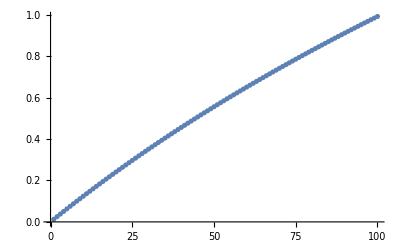

迭代步数 = 1879

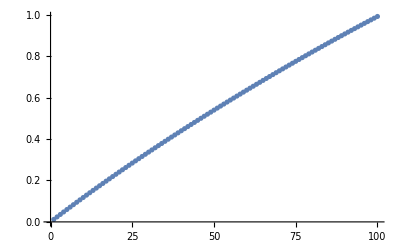

迭代步数 = 1391

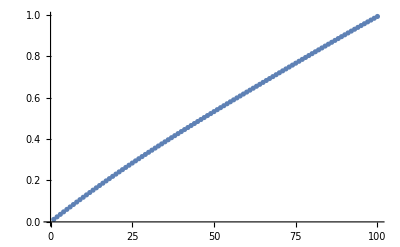

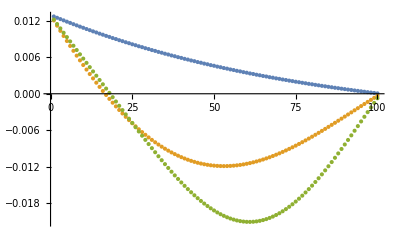

```mathematica
ListPlot[jacobiSolution[1]=jacobiSolve[1,1/100,0.5`20]]
ListPlot[gsSolution[1]=gsSolve[1,1/100,0.5`20]]
ListPlot[sorSolution[1]=sorSolve[1,1/100,0.5`20,0.86`20]]
ListPlot[{jacobiSolution[1]-exactSolution[1],gsSolution[1]-exactSolution[1],sorSolution[1]-exactSolution[1]}]
```

误差的L2范数为：

```mathematica
Norm/@{jacobiSolution[1]-exactSolution[1],gsSolution[1]-exactSolution[1],sorSolution[1]-exactSolution[1]}
```

{0.0633007,0.0823268,0.137029}

可以看到，jacobi算法虽然收敛较慢，但是最后精确度反而较大。而G-S法受制于舍入误差，最后计算时解向量变化很慢。

### 其他 ϵ 值的情况

对于 ϵ 为 0.1，0.001，0.0001等值，考虑问题如下。代码几乎相同，所需指出的是：

ϵ 值越小，解在 x 接近于零时变化越快。此时迭代法很难得到精度很高的解

与精确值差距较大的地方几乎都在 x 接近零处，之后随着解变化更慢，不论相对误差还是绝对误差均很小

误差向量的范数此时作用不大：因为所有的大误差都是前端贡献的，此时绝对误差图像更有价值。

迭代步数 = 5986

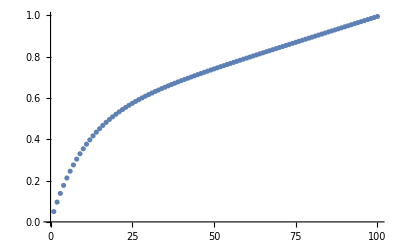

迭代步数 = 1844

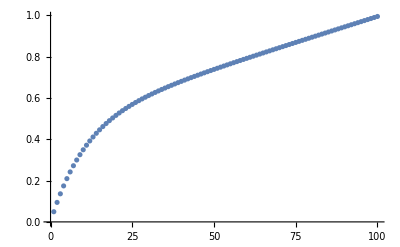

迭代步数 = 2309

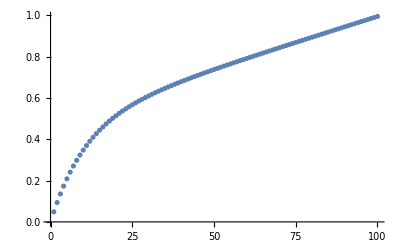

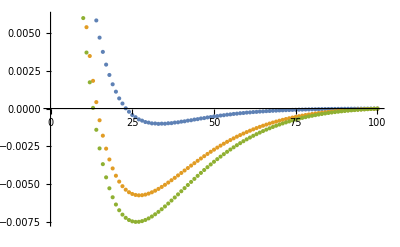

{0.097837,0.0935896,0.0945604}

```mathematica
ϵ=0.1;
ListPlot[jacobiSolution[ϵ]=jacobiSolve[ϵ,1/100,0.5`20]]
ListPlot[gsSolution[ϵ]=gsSolve[ϵ,1/100,0.5`20]]
ListPlot[sorSolution[ϵ]=sorSolve[ϵ,1/100,0.5`20,0.86`20]]
ListPlot[{jacobiSolution[ϵ]-exactSolution[ϵ],gsSolution[ϵ]-exactSolution[ϵ],sorSolution[ϵ]-exactSolution[ϵ]}]
Norm/@{jacobiSolution[ϵ]-exactSolution[ϵ],gsSolution[ϵ]-exactSolution[ϵ],sorSolution[ϵ]-exactSolution[ϵ]}
```

迭代步数 = 537

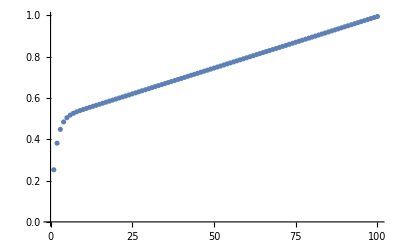

迭代步数 = 294

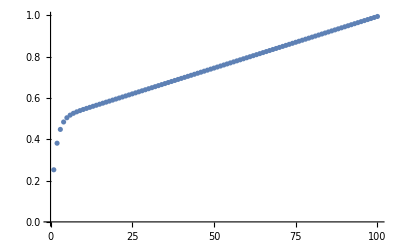

迭代步数 = 375

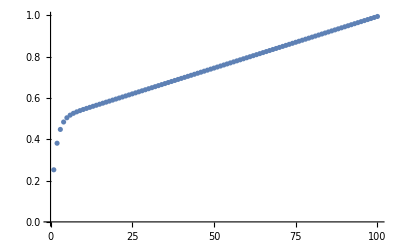

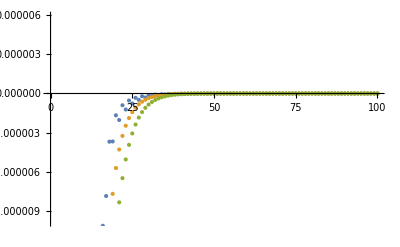

{0.259814,0.259685,0.259613}

```mathematica
ϵ=0.01;
ListPlot[jacobiSolution[ϵ]=jacobiSolve[ϵ,1/100,0.5`20]]
ListPlot[gsSolution[ϵ]=gsSolve[ϵ,1/100,0.5`20]]
ListPlot[sorSolution[ϵ]=sorSolve[ϵ,1/100,0.5`20,0.86`20]]
ListPlot[{jacobiSolution[ϵ]-exactSolution[ϵ],gsSolution[ϵ]-exactSolution[ϵ],sorSolution[ϵ]-exactSolution[ϵ]}]
Norm/@{jacobiSolution[ϵ]-exactSolution[ϵ],gsSolution[ϵ]-exactSolution[ϵ],sorSolution[ϵ]-exactSolution[ϵ]}
```

迭代步数 = 115

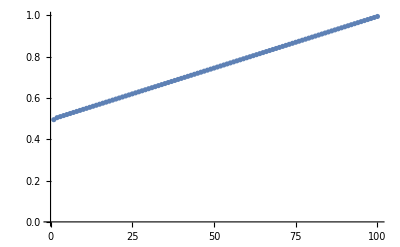

迭代步数 = 108

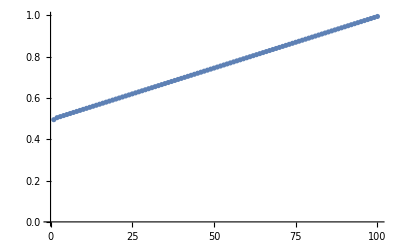

迭代步数 = 139

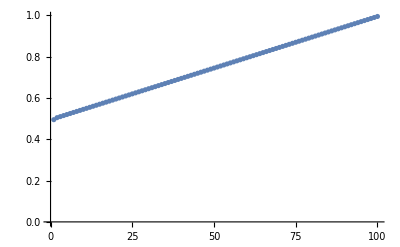

General::munfl: Exp[-10000.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

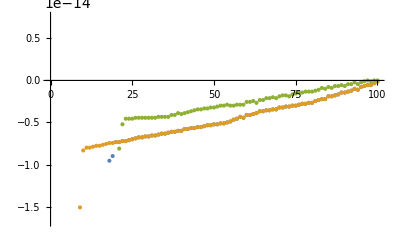

{0.495088,0.495097,0.495079}

```mathematica
ϵ=0.0001;
ListPlot[jacobiSolution[ϵ]=jacobiSolve[ϵ,1/100,0.5`20]]
ListPlot[gsSolution[ϵ]=gsSolve[ϵ,1/100,0.5`20]]
ListPlot[sorSolution[ϵ]=sorSolve[ϵ,1/100,0.5`20,0.86`20]]
ListPlot[{jacobiSolution[ϵ]-exactSolution[ϵ],gsSolution[ϵ]-exactSolution[ϵ],sorSolution[ϵ]-exactSolution[ϵ]}]
Norm/@{jacobiSolution[ϵ]-exactSolution[ϵ],gsSolution[ϵ]-exactSolution[ϵ],sorSolution[ϵ]-exactSolution[ϵ]}
```